```mathematica
Solve[Q == α (1-m)^2 + (1-α)Q (1-m)^2,Q]
Qe=Q/.%⟦1⟧//FullSimplify
Qe/.α->1/n//FullSimplify
```

{{Q→((-1+m)^2 α)/(2 m-m^2+α-2 m α+m^2 α)}}

((-1+m)^2 α)/((-2+m) m (-1+α)+α)

-(-1+m)^2/(-1+(-2+m) m (-1+n))

```mathematica
W = -c - (b-c)(1-m)^2/n+Q*(b-(b-c)(n-1)(1-m)^2/n);
Collect[W, b,FullSimplify]
```

(c (1-2 m+m^2-n+(-1+m)^2 (-1+n) Q))/n+(b (-1+Q-(-2+m) m (1+(-1+n) Q)))/n

```mathematica
κ=(-1+Q-(-2+m) m (1+(-1+n) Q))/n/(-(1-2 m+m^2-n+(-1+m)^2 (-1+n) Q)/n)//FullSimplify
```

(1-Q+(-2+m) m (1+(-1+n) Q))/(1-2 m+m^2-n+(-1+m)^2 (-1+n) Q)

```mathematica
WW=W/.Q->Qe//FullSimplify
WW/.α->1/n//FullSimplify
```

-c-((b-c) (-1+m)^2)/n+((-1+m)^2 (b-((b-c) (-1+m)^2 (-1+n))/n) α)/((-2+m) m (-1+α)+α)

-(c (-2+m) m n)/(-1+(-2+m) m (-1+n))

```mathematica
(-c (2-m) m n)/(1+(2-m) m (n-1)) - (-(c (-2+m) m n)/(-1+(-2+m) m (-1+n)))//FullSimplify
```

0

```mathematica
WW/.n->4/.α->1/2//FullSimplify
```

((-2+m) m (b (-1+m)^2-c (5+(-2+m) m)))/(2 (-1+(-2+m) m))

```mathematica
M1=(ND-1)/(1-((1-μ)^2(ND(1-m)-1)^2)/(ND-1)^2); M2=1/(1-(1-μ)^2);
QWF=(-ND+M1+M2)/((n-1)ND+M1+M2);
Limit[QWF,ND->∞]
QWF0=Limit[%,μ->0]//FullSimplify
```

-((-1+m)^2 (-1+μ)^2)/(-1-2 m (-1+n) (-1+μ)^2+m^2 (-1+n) (-1+μ)^2-2 (-1+n) μ+(-1+n) μ^2)

-(-1+m)^2/(-1+(-2+m) m (-1+n))

```mathematica
κ/.Q->QWF0//FullSimplify
```

0

```mathematica
κ/.Q->Qe//FullSimplify
```

((-1+m)^2 (-1+n α))/(-1+n+n α+(-2+m) m (-1+n α))

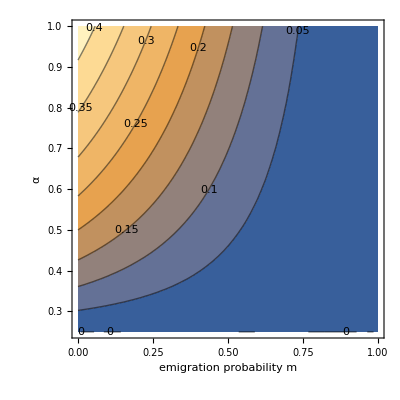

```mathematica
myn =4;
ContourPlot[κ/.Q->Qe/.n->myn,{m,0.00001,1},{α,1/myn,1},ContourLabels->True,FrameLabel->{"emigration probability m", "α"}]
```

## Finite population

Notation : 
(x=y): x=y;
(x,y): x and y are two different sites in the same deme,
x,y: x and y are two sites in different demes.

```mathematica
QQin = (1-μ)^2(1*dself*din*1*pself+(* (i=k=l,j)
*)1*dself*dself*Qin *pin+ (* (i=k,j=l)
*)(n-2)*dself*din*Qin*pin+(* (i=k,j,l)
*)(n d-n)*dself*dout*Qout*pin+(* (i=k,j),l

*)1*din*din*Qin*pin+(* (i=l,j=k)
*)1*din*dself*1*pself+(* (i,j=k=l)
*)(n-2)*din*din*Qin*pin+(* (i,j=k,l)
*)(d n -n)*din*dout*Qout*pout+(* (i,j=k),l

*)(n-2)*1*din*din*Qin*pin+(* (i=l,j,k)
*)(n-2)*1*din*dself*Qin*pin+(* (i,j=l,k)
*)(n-2)*1*din*din*1*pself+(* (i,j,k=l)
*)(n-2)*(n-3)*din*din*Qin*pin+(* (i,j,k,l)
*)(n-2)*(n d-n)*din*dout*Qout*pout+(*(i,j,k),l

*)(n d - n)*1*dout*din*Qout*pout+(* (i=l,j),k
*)(n d - n)*1*dout*dself*Qout*pout+(* (i,j=l),k
*)(n d - n)*(n-2)*dout*din*Qout*pout+(* (i,j,l),k
*)(n d - n)*1*dout*dout*1*pself+(* (i,j),(k=l)
*)(n d - n)*(n-1)*dout*dout*Qin*pin+(* (i,j),(k,l)
*)(n d - n)*(n d -2 n)*dout*dout*Qout*pout) (* (i,j),k,l
*);
```

```mathematica
QQout=(1-μ)^2(1*1*dself*dout*1*pself+(* (i=k=l),(j)
*)1*(n-1)*dself*dout*Qin*pin+(* (i=k,l),(j)
*)1*1*dself*dself*Qout*pout+(* (i=k),(j=l)
*)1*(n-1)*dself*din*Qout*pout+(* (i=k),(j,l)
*)1*(n d -2n)*dself*dout*Qout*pout+(* (i=k),(j),l

*)(n-1)*1*din*dout*Qin*pin+(* (i=l,k),(j)
*)(n-1)*1*din*dout*1*p+(* (i,k=l),(j)
*)(n-1)*(n-2)*din*dout*Qin*pin+(* (i,k,l),(j)
*)(n-1)*1*din*dself*Qout*pout+(* (i,k),(j=l)
*)(n-1)*(n-1)*din*din*Qout*pout+(* (i,k),(j,l)
*)(n-1)*(n d -2n)*din*dout*Qout*pout+(* (i,k),(j),l

*)1*1*dout*dout*Qout*pout+(* (i=l),(j=k)
*)1*(n-1)*dout*dout*Qout*pout+(* (i,l),(j=k)
*)1*1*dout*dself*1*pself+(* (i),(j=k=l)
*)1*(n-1)*dout*din*Qin*pin+(* (i),(j=k,l)
*)1*(n d - 2n)*dout*dout*Qout*pout+(* (i),(j=k),l

*)(n-1)*1*dout*dout*Qout*pout+(* (i=l),(j,k)
*)(n-1)*(n-1)*dout*dout*Qout*pout+(* (i,l),(j,k)
*)(n-1)*1*dout*dself*Qin*pin+(* (i),(j=l,k)
*)(n-1)*1*dout*din*1*pself+(* (i),(j,k=l)
*)(n-1)*(n-2)*dout*din*Qin*pin+(* (i),(j,k,l)
*)(n-1)*(n d -2n)*dout*dout*Qout*pout+(* (i),(j,k),l

*)(n d-2n)*1*dout*dout*Qout*pout+(* (i=l),(j),(k)
*)(n d -2n)*(n-1)*dout*dout*Qout*pout+(* (i,l),(j),(k)
*)(n d -2n)*1*dout*dself*Qout*pout+(* (i),(j=l),(k)
*)(n d -2n)*(n-1)*dout*din*Qout*pout+(* (i),(j,l),(k)
*)(n d -2n)*1*dout*dout*1*pself+(* (i),(j),(k=l)
*)(n d -2n)*(n-1)dout*dout*Qin*pin+(* (i),(j),(k,l)
*)(n d -2n)*(n d -3n)*dout*dout*Qout*pout) (*(i),(j),(k),l
*);
```

```mathematica
sol=Solve[{Qin==QQin, Qout==QQout}, {Qin, Qout}]/.{dself->din}/.{din->(1-m)/n, dout->m/(n d-n)}//FullSimplify
```

$Aborted

```mathematica
sol0=sol/.p->1//FullSimplify
```

{{Qin→-(((-1+μ)^2 (2 m+d (-2+m) m-2 (1+d (-1+m))^2 μ+(1+d (-1+m))^2 μ^2))/((-1+d)^2 (-2+μ) μ (-1+(-1+n) (-2+μ) μ)-2 (-1+d) m (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+d m^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ))),Qout→-(((2+d (-2+m)) m (-1+μ)^2)/((-1+d)^2 (-2+μ) μ (-1+(-1+n) (-2+μ) μ)-2 (-1+d) m (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+d m^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)))}}

```mathematica
Limit[Qout/.sol0⟦1⟧,d->∞]//FullSimplify
```

0

```mathematica
Limit[Qin/.sol0⟦1⟧,d->∞]//FullSimplify
Limit[%,μ->0]//FullSimplify
```

-((-1+m)^2 (-1+μ)^2)/(-1-2 m (-1+n) (-1+μ)^2+m^2 (-1+n) (-1+μ)^2+(-1+n) (-2+μ) μ)

-(-1+m)^2/(-1+(-2+m) m (-1+n))

```mathematica
RR=(Qin-Qout)/(1-Qout)/.sol⟦1⟧//FullSimplify
```

-(((1+d (-1+m))^2 p (-1+p^2 (-1+μ)^2) (-1+μ)^2)/((n (-1+p (-1+μ)) (1+p (-1+μ)) (1+d (-1+(-1+m) p (-1+μ))+p (-1+μ)) (-1+d (1+(-1+m) p (-1+μ))+p (-1+μ))-p^2 (-1+μ)^2 (-1+2 m+p^2+d (2-4 m+m^2+2 (-1+m) p^2+d (-1+m)^2 (-1+p^2))-2 (1+d (-1+m))^2 p^2 μ+(1+d (-1+m))^2 p^2 μ^2)) (1+((2+d (-2+m)) m p (-1+μ)^2)/(n (-1+p (-1+μ)) (1+p (-1+μ)) (1+d (-1+(-1+m) p (-1+μ))+p (-1+μ)) (-1+d (1+(-1+m) p (-1+μ))+p (-1+μ))-p^2 (-1+μ)^2 (-1+2 m+p^2+d (2-4 m+m^2+2 (-1+m) p^2+d (-1+m)^2 (-1+p^2))-2 (1+d (-1+m))^2 p^2 μ+(1+d (-1+m))^2 p^2 μ^2)))))

{d→15,n→4,b→15,c→1}

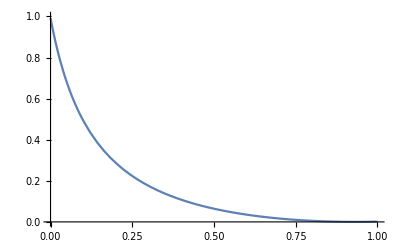

```mathematica
prms={d->15,n->4,b->15,c->1}
Plot[RR/.{d->15,p->1,μ->0.001,n->4},{m,0,1},PlotRange->{0,1}]
```

```mathematica
CWF=(1-μ)c+(b-c)(1-μ)((1-m)^2/n+m^2/(n d-n));
BWF=(1-μ)b-(n-1)(b-c)(1-μ)((1-m)^2/n+m^2/(n d-n));
```

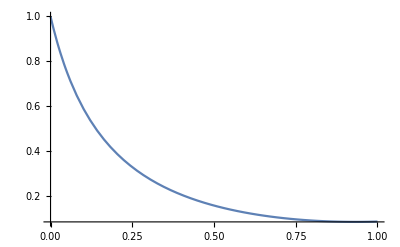

```mathematica
Plot[CWF/BWF/.prms/.μ->theμ,{m,0,1}]
```

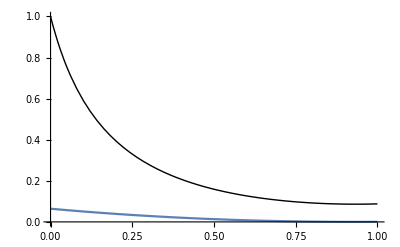

```mathematica
theμ=0.01;thep=0.25;
Show[Plot[CWF/BWF/.prms/.μ->theμ,{m,0,1},PlotStyle->{Thick,Black}],Plot[RR/.prms/.μ->theμ/.p->thep,{m,0,1},PlotRange->{All,{0,1}}],PlotRange->{All,{0,1}},AxesOrigin->{0,0}]
```

```mathematica
QQin/.dout->0/.dself->din
```

(2 din^2 p+din^2 (-2+n) p+2 din^2 p^2 Qin+4 din^2 (-2+n) p^2 Qin+din^2 (-3+n) (-2+n) p^2 Qin) (1-μ)^2

```mathematica
QQout/.dout->0//FullSimplify
```

(dself+din (-1+n))^2 pout Qout (-1+μ)^2

```mathematica
QQin/.dout->0
```

(2 din dself p+din^2 (-2+n) p+din^2 p^2 Qin+dself^2 p^2 Qin+2 din^2 (-2+n) p^2 Qin+2 din dself (-2+n) p^2 Qin+din^2 (-3+n) (-2+n) p^2 Qin) (1-μ)^2

```mathematica
QG=Qin/.Solve[(QQin/.dout-> 0/.dself->din/.din->(1-m)/n)==Qin,Qin]⟦1⟧//FullSimplify
```

-((-1+m)^2 pself (-1+μ)^2)/(n (-1+(-1+m)^2 pin (-1+μ)^2)-(-1+m)^2 pin (-1+μ)^2)

α=pself/n;1-α=((n-1)pin)/n;

```mathematica
QGa=QG/.pself->n α/.pin->n (1-α)/(n-1)//FullSimplify
%/.μ->0//FullSimplify
```

((-1+m)^2 α (-1+μ)^2)/(-2 m (-1+α) (-1+μ)^2+m^2 (-1+α) (-1+μ)^2+α (-1+μ)^2-(-2+μ) μ)

((-1+m)^2 α)/((-2+m) m (-1+α)+α)

```mathematica
α+(1-α)(1-(1-m)^2)+2(1-(1-m)^2)//FullSimplify
```

(-2+m) m (-3+α)+α

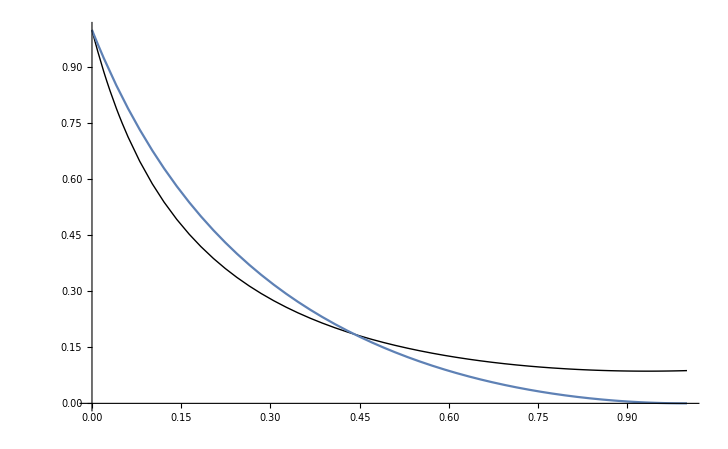

```mathematica
theμ=0.0;thep=0.5;
Show[Plot[CWF/BWF/.prms/.μ->theμ,{m,0,1},PlotStyle->{Thick,Black}],Plot[QGa/.prms/.μ->theμ/.α->thep,{m,0,1},PlotRange->{All,{0,1}}],PlotRange->{All,{0,1}},AxesOrigin->{0,0}]
```